1 - 5 Components and length
Find the components of the vector v with initial point P and terminal point Q. Find |v|. Sketch |v|. Find the unit vector u in the direction of v.

1.  P : (1, 1, 0), Q : (6, 2, 0)

```mathematica
ClearAll["Global`*"]
```

Below: reposition vector tail to origin.

```mathematica
pP={1,1,0};qQ={6,2,0};
vec=qQ-pP
```

{5,1,0}

Below: calculate length of vector.

```mathematica
euc1=Norm[vec]
```

√26

Below: find normalized version of vector.

```mathematica
euc2=Normalize[vec]
```

{5/(√26),1/(√26),0}

The green cells above match the answers in the text.

Below: find normalized version in decimal form.

```mathematica
euc3=N[Normalize[vec],4]
```

{0.9806,0.1961,0}

```mathematica
pad=N[euc3+{.3,.3,.3},4]
```

{1.28058,0.496116,0.3}

```mathematica
Graphics3D[{Opacity[1],Gray,PointSize[.015],Arrowheads[{{.04,.88}}],Arrow[Tube[{{0,-4,0},{0,4,0}},.01]],Arrow[Tube[{{0,0,-4},{0,0,4}},.01]],
Arrow[Tube[{{-4,0,0},{4,0,0}},.01]],Text["+x",{3.3,0,0}],Text["+y",{0,3.3,0}],Text["+z",{0,0,3.3}],Text["{0.9805,0.1961,0.}",{1.2805,0.4961,0.3}],Text[Style["",Small,Black]],Dashing[Tiny],Line[{{0,0,0},{5/(√26),1/(√26),0}}],Line[{{5/(√26),0,0},{5/(√26),1/(√26),0}}],Red,Point[{5/(√26),1/(√26),0}]},Axes->None,AxesOrigin->{0,0,0},ViewPoint->{1.5,1.5,-1},Boxed->False,Ticks->Automatic,PlotRange->{{-3,3},{-3,3},{-3,3}},ImageSize->350]
```

-Graphics3D-

3.  P : (-3.0, 4.0, -0.5), Q : (5.5, 0, 1.2)

```mathematica
ClearAll["Global`*"]
```

Below: reposition vector tail to origin.

```mathematica
pP={-3.0,4.0,-0.5};qQ={5.5,0,1.2};
vec=qQ-pP
```

{8.5,-4.,1.7}

Below: calculate length of vector.

```mathematica
euc1=Norm[vec]
```

9.54673

```mathematica
PossibleZeroQ[Chop[euc1]-Chop[√91.14]]
```

True

Below: find normalized version of vector.

```mathematica
euc2=N[Normalize[vec],4]
```

{0.890357,-0.418992,0.178071}

```mathematica
pad=N[euc2+{.3,.3,.3},4]
```

{1.19036,-0.118992,0.478071}

The green cells above match the answers in the text.

```mathematica
Graphics3D[{Opacity[1],Gray,PointSize[.015],Arrowheads[{{.04,.88}}],Arrow[Tube[{{0,-4,0},{0,4,0}},.01]],Arrow[Tube[{{0,0,-4},{0,0,4}},.01]],
Arrow[Tube[{{-4,0,0},{4,0,0}},.01]],Text["+x",{3.3,0,0}],Text["+y",{0,3.3,0}],Text["+z",{0,0,3.3}],Text["{-0.5970,0.7960,-0.0995}",{-0.2970,1.0960,0.2004}],Text[Style["",Small,Black]],Dashing[Tiny],Line[{{0,0,0},{-0.5970,0.7960,-0.0995}}],Line[{{0,0,0},{-0.5970,0.7960,0}}],Line[{{-0.5970,0.7960,0},{-0.5970,0.7960,-0.0995}}],Red,Point[{-0.5970,0.7960,-0.0995}]},Axes->None,AxesOrigin->{0,0,0},ViewPoint->{1.5,1.5,-1},Boxed->False,Ticks->Automatic,PlotRange->{{-3,3},{-3,3},{-3,3}},ImageSize->400]
```

-Graphics3D-

5.  P : (0, 0, 0), Q : (2, 1, -2)

```mathematica
ClearAll["Global`*"]
```

Below: reposition vector tail to origin.

```mathematica
pP={0,0,0};qQ={2,1,-2};
vec=qQ-pP
```

{2,1,-2}

Below: calculate length of vector.

```mathematica
euc1=Norm[vec]
```

3

Below: find normalized version of vector.

```mathematica
euc2=N[Chop[Normalize[vec],10^-4]]
```

{0.666667,0.333333,-0.666667}

```mathematica
pad=N[euc2+{.3,.3,.3},4]
```

{0.966667,0.633333,-0.366667}

The green cells above match the answers in the text (no entry for vector length).

```mathematica
Graphics3D[{Opacity[1],Gray,PointSize[.015],Arrowheads[{{.04,.88}}],Arrow[Tube[{{0,-4,0},{0,4,0}},.01]],Arrow[Tube[{{0,0,-4},{0,0,4}},.01]],
Arrow[Tube[{{-4,0,0},{4,0,0}},.01]],Text["+x",{3.3,0,0}],Text["+y",{0,3.3,0}],Text["+z",{0,0,3.3}],Text["{.6666,0.3333,-0.6666}",{0.9666,0.6333,-0.3666}],Text[Style["",Small,Black]],Dashing[Tiny],Line[{{0,0,0},{.6666,0.3333,-0.6666}}],Line[{{0,0,0},{.6666,0.3333,0}}],Line[{{.6666,0.3333,0},{.6666,0.3333,-0.6666}}],Red,Point[{.6666,0.3333,-0.6666}]},Axes->None,AxesOrigin->{0,0,0},ViewPoint->{1.5,1.5,-1},Boxed->False,Ticks->Automatic,PlotRange->{{-3,3},{-3,3},{-3,3}},ImageSize->400]
```

-Graphics3D-

6 - 10 Find the terminal point Q of the vector v with components as given and initial point P. Find |v|.

7.  1/2, 3, -1/4; P: (7/2, -3, 3/4)

```mathematica
ClearAll["Global`*"]
```

```mathematica
vec={1/2,3,-1/4}; po={7/2,-3,3/4};
que=vec+po
```

{4,0,1/2}

```mathematica
e1=Norm[vec+po]
```

(√65)/2

```mathematica
FullSimplify[(√65)/2==√16.25]
```

True

The green cells above match the answers in the text.

9.  6, 1, -4; P : (-6, -1, -4)

```mathematica
ClearAll["Global`*"]
```

```mathematica
vec={6,1,-4}; po={-6,-1,-4};
que=vec+po
```

{0,0,-8}

```mathematica
e1=Norm[que]
```

8

The green cells above match the answers in the text.

11 - 18 Addition, scalar multiplication
Let a = {3, 2, 0} = 3 i + 2 j; b = {-4, 6, 0} = 4 i + 6 j; c = {5, -1, 8} = 5 i - j + 8 k, d = {0, 0, 4} = 4 k
Find

11.  2a, 1/2 a, -a

```mathematica
ClearAll["Global`*"]
```

```mathematica
aa={3,2,0};bb={-4,6,0};cc={5,-1,8};dd={0,0,4}
```

{0,0,4}

```mathematica
2 aa
```

{6,4,0}

```mathematica
1/2 aa
```

{3/2,1,0}

```mathematica
-aa
```

{-3,-2,0}

The green cells above match the answers in the text.

13.  b + c, c + b

```mathematica
bb+cc
```

{1,5,8}

```mathematica
cc+bb
```

{1,5,8}

15.  7 (c - b), 7 c - 7 b

```mathematica
7 (cc+bb)
```

{7,35,56}

```mathematica
7 (cc-bb)
```

{63,-49,56}

17.  (7 - 3) a, 7 a - 3 a

```mathematica
(7-3)aa
```

{12,8,0}

```mathematica
7 aa-3 aa
```

{12,8,0}

The green cells above match the answers in the text.

21 - 25 Forces, resultant
Find the resultant in terms of components and its magnitude.

21.  p = {2, 3, 0}, q = {0, 6, 1}, u = {2, 0, -4}

```mathematica
res={2+0+2,3+6+0,0+1-4}
```

{4,9,-3}

```mathematica
Norm[res]
```

√106

```mathematica
matt=({{2, 3, 0}, {0, 6, 1}, {2, 0, -4}})
```

{{2,3,0},{0,6,1},{2,0,-4}}

```mathematica
e2=RowReduce[matt]
```

{{1,0,0},{0,1,0},{0,0,1}}

Above: the reduced echelon form says that the three vectors are linearly independent. Therefore there is no possibility of finding factors which express one in terms of the other two.

23.  u={18, -1, 0}, v={1/2, 0, 4/3}, w={-17/2,1,11/3}

```mathematica
res={8+1/2-17/2,-1+0+1,0+4/3+11/3}
```

{0,0,5}

```mathematica
Norm[res]
```

5

```mathematica
mat=({{8, -1, 0}, {1/2, 0, 4/3}, {-17/2, 1, 11/3}})
```

{{8,-1,0},{1/2,0,4/3},{-17/2,1,11/3}}

```mathematica
e1=RowReduce[mat]
```

{{1,0,0},{0,1,0},{0,0,1}}

Above: the reduced echelon form says that the three vectors are linearly independent. Therefore there is no possibility of finding factors which express one in terms of the other two.

25.  u = {3, 1, -6}, v = {0, 2, 5}, w = {3, -1, -13}

```mathematica
res={3+0+3,1+2-1,-6+5-13}
```

{6,2,-14}

```mathematica
Norm[res]
```

2 √59

```mathematica
mattt=({{3, 1, -6}, {0, 2, 5}, {3, -1, -13}})
```

{{3,1,-6},{0,2,5},{3,-1,-13}}

```mathematica
RowReduce[mattt]
```

{{1,0,0},{0,1,0},{0,0,1}}

Above: for this one, the text says the result is 2u. I don’t think that is a correct statement. In fact, the reduced echelon form says that the three vectors are linearly independent. Therefore is it not doubtful that I can find factors which express one in terms of the other two?

26 - 37 Forces, velocities

27. Find p such that u, v, w in problem 23 and p are in equilibrium.

From problem 37, it is understood that vectors, considered as forces, are in equilibrium when they form a ‘force polygon.’ This polygon will have to be 4-sided. From the s.m., I find that “. . . “Equilibrium” means that the resultant of the given forces is the zero vector.” Meaning I need to find p such that u+v+w+p=0.

```mathematica
ClearAll["Global`*"]
```

```mathematica
uu={8,-1,0};vv={1/2,0,4/3};ww={-17/2,1,11/3}
```

{-17/2,1,11/3}

```mathematica
pp=-(uu+vv+ww)
```

{0,0,-5}

29. Restricted resultant. Find all v such that the resultant of v, p, q, u with p, q, u as in problem 21 is parallel to the xy-plane.

The resultant vector in problem 21 was {4,9,-3}. So any vector of the form {x,y,-3} will be parallel to the xy-plane when added to the resultant of problem 21.

31. For what k is the resultant of {2, 0, -7}, {1, 2, -3}, and {0, 3, k} parallel to the xy-plane?

```mathematica
res1={2+1,0+2,-3-7}
```

{3,2,-10}

```mathematica
k=10
```

10

The green cells above match the answers in the text.

32. If |p| = 6 and |q|= 4, what can you say about the magnitude and direction of the resultant? Can you think of an application to robotics?

33. Same question as in problem 32 if |p| = 9, |q| = 6, |u| = 3.

Comprising three cloud spheres. Any resulting magnitude greater than or equal to zero and less than or equal to 18. Any octant.

34. Relative velocity. If airplanes A and B are moving southwest with speeds |v_A| = 550 mph, and northwest with speed |v_B| = 450 mph, respectively, what is the relative velocity v = v_B - v_A of B with respect to A?

```mathematica
ClearAll["Global`*"]
```

```mathematica
N[Solve[2 aa^2==550^2],4]
```

{{aa→-388.9},{aa→388.9}}

```mathematica
aavec={-388.9,-388.9}
```

{-388.9,-388.9}

```mathematica
N[Solve[2 bb^2==450^2],4]
```

{{bb→-318.2},{bb→318.2}}

```mathematica
bbvec={-318.2,318.2}
```

{-318.2,318.2}

```mathematica
bbvec-aavec
```

{70.7,707.1}

```mathematica
Norm[bbvec-aavec]
```

710.626

The relative velocity of bbvec with respect to aavec is 70.7 mph east, 707.1 mph north.

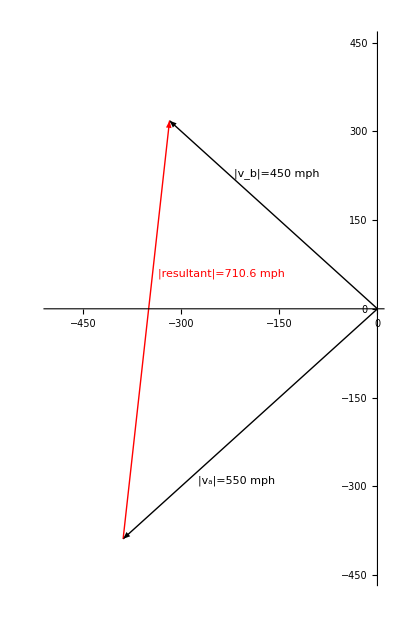

```mathematica
Plot[ Sin[x],{x,-500,0},PlotStyle->{White, Thickness[0.001]},PlotRange->{-450,450},AspectRatio->1.6,Epilog->{{Arrow[{{0,0},{-318,318}}],Text["|v_b|=450 mph",{-220
,220},{-1,-1}]},{Arrow[{{0,0},{-389,-389}}],Text["|v_a|=550 mph",{-275,-300},{-1,-1}]},{Red,Arrow[{{-389,-389},{-318,318}}],Text["|resultant|=710.6 mph",{-335,50},{-1,-1}]}}]
```

35.  Same question as in problem 34 for two ships moving northeast with speed |v_A| = 22 knots and west with speed |v_B| = 19 knots.

```mathematica
ClearAll["Global`*"]
```

```mathematica
N[Solve[2 as^2==22^2],4]
```

{{as→-15.56},{as→15.56}}

```mathematica
asvec={15.56,15.56}
```

{15.56,15.56}

```mathematica
N[Solve[ bs^2==19^2],4]
```

{{bs→-19.},{bs→19.}}

```mathematica
bsvec={-19,0}
```

{-19,0}

The problem doesn’t say what the perspective is, let’s say I want velocity of ship b with respect to ship a.

```mathematica
resulta=bsvec-asvec
```

{-34.56,-15.56}

The relative velocity of ship b with respect to ship a is 34.6 knots west, 15.6 knots south.

```mathematica
Norm[resulta]
```

37.9013

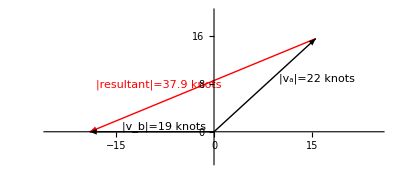

```mathematica
Plot[ Sin[x],{x,-25,25},PlotStyle->{White, Thickness[0.001]},PlotRange->{-5,20},AspectRatio->.45,Epilog->{{Red,Arrow[{{15.56,15.56},{-19,0}}],Text["|resultant|=37.9 knots",{-18,7},{-1,-1}]},{Arrow[{{0,0},{-19,0}}],Text["|v_b|=19 knots",{-14,0},{-1,-1}]},{Arrow[{{0,0},{15.56,15.56}}],Text["|v_a|=22 knots",{10,8},{-1,-1}]}}]
```

```mathematica
N[{-19-22/√2,-22/√2}]
```

{-34.5563,-15.5563}

The green cells above match the answers in the text.

37. Force polygon. Truss. Find the forces in the system of two rods (truss) in the figure, where |p| = 1000 nt. Hint. Forces in equilibrium form a polygon, the force polygon.

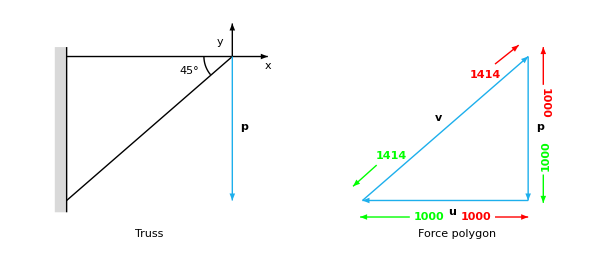

```mathematica
bl=RGBColor[29/255,175/255,236/255];
Graphics[{(*{LightGray,Table[Line[{{n,-1},{n,3.5}}],{n,0,12,0.2}]},{LightGray,Table[Line[{{0,n},{12,n}}],{n,-1,3.5,0.2}]},*){RGBColor[0.85,0.85,0.85],Rectangle[{0,0},{0.25,3.5}]},{Arrowheads[0.03],Arrow[{{0.25,3.3},{4.5,3.3}}]},{Arrowheads[0.03],Arrow[{{3.75,3.3},{3.75,4}}]},{Line[{{0.25,0},{0.25,3.5}}]},{Line[{{0.25,0.25},{3.75,3.3}}]},{bl,Thick,Arrowheads[0.03],Arrow[{{3.75,3.3},{3.75,0.25}}]},{Circle[{3.75,3.3},0.6,{-π,-π+0.7}]},{bl,Thick,Arrowheads[0.03],Arrow[{{10,3.3},{10,0.25}}]},{bl,Thick,Arrowheads[0.03],Arrow[{{10,0.25},{6.5,0.25}}]},{bl,Thick,Arrowheads[0.03],Arrow[{{6.5,0.25},{10,3.3}}]},{Text[Style["x",Medium],{4.5,3.1}]},{Text[Style["y",Medium],{3.5,3.6}]},{Text[Style["45°",Medium],{2.85,3}]},{Text[Style["p",Medium,Bold],{4,1.8}]},{Text[Style["v",Medium,Bold],{8.1,2}]},{Text[Style["p",Medium,Bold],{10.25,1.8}]},{Text[Style["u",Medium,Bold],{8.4,0}]},{Text[Style["Force polygon",Medium,Italic],{8.5,-0.45}]},{Text[Style["Truss",Medium,Italic],{2,-0.45}]},{Green,Arrowheads[0.025],Thick,Arrow[{{6.8,1},{6.3,0.55}}]},{Green,Text[Style["1414",Medium,Bold],{7.1,1.2},Automatic,{1,1}]},{Red,Arrowheads[0.025],Thick,Arrow[{{9.3,3.14},{9.8,3.54}}]},{Red,Text[Style["1414",Medium,Bold],{9.1,2.9},Automatic,{1,1}]},{Red,Text[Style["1000",Medium,Bold],{10.35,2.3},Automatic,{0,-1}]},{Red,Arrowheads[0.025],Thick,Arrow[{{10.32,2.7},{10.32,3.5}}]},{Green,Text[Style["1000",Medium,Bold],{10.36,1.2},Automatic,{0,1}]},{Green,Arrowheads[0.025],Thick,Arrow[{{10.32,0.8},{10.32,0.2}}]},{Green,Text[Style["1000",Medium,Bold],{7.9,-0.1}]},{Green,Arrowheads[0.025],Thick,Arrow[{{7.5,-0.1},{6.45,-0.1}}]},{Red,Text[Style["1000",Medium,Bold],{8.9,-0.1}]},{Red,Arrowheads[0.025],Thick,Arrow[{{9.3,-0.1},{10,-0.1}}]}},Axes->False,ImageSize->600]
```

```mathematica
ClearAll["Global`*"]
```

This looks like a simple problem that could be taken care of in a line or two. There is the older approach set out at https://rip94550.wordpress.com/2012/03/19/trusses-example-1/. This blogsite on applied math is directed/written/curated by Rip and appears to use Mathematica 8. The details still appear to work okay. However, the problem differs slightly from the current one.

There is also the YouTube video at https://www.youtube.com/watch?v=H60Q70FZI9M, uploaded by MrClean. It has forces directed in the same sense as the present problem. I applied analogous forces to the force polygon above, green for imposed force, red for reaction force. All forces cancel, meaning the truss remains stationary. For some reason the text answer does not mention the forces in v. Maybe a force polygon does not work the same as the method of joints.